Lecture Intro AceFEM
Notebook for Exercises 
Created by Michele Marino, Department of Civil Engineering and Computer Science, University of Rome Tor Vergata, Italy
Date: 02 November 2021 - Contact: m.marino@ing.uniroma2.it

# Element Codes

## T1LE - Linear elasticity

### Initialization

```mathematica
<<AceGen`;
SMSInitialize["T1LE","Environment"-> "AceFEM","Mode"-> "Optimal"];
SMSTemplate["SMSTopology"->"T1",
(*Numerical Integration*) "SMSDefaultIntegrationCode"->35,
(*35 -Graphics-*)
(*Initialize domain data for material parameters*)
"SMSDomainDataNames"-> {"E -Young","ν -Poisson"}, "SMSDefaultData" -> {1,0.49},
(*Expected symmetry in tangent stiffness*)
"SMSSymmetricTangent"->True,
"SMSNoElementData" -> 3];

RelevantNumbers[]:=(
nen=SMSNoNodes; 
ndim=SMSNoDimensions; 
ndof=SMSNoDOFGlobal;
nip=SMSIO["No. integration points"];
(* Equivalent to: SMSInteger[es$$["id", "NoIntPoints"]] *)
)
```

### Element definitions

```mathematica
ElementDefinitions[Ig_]:=(
(*MATERIAL AND ELEMENT DATA*)
{Ee,ν}⊨SMSIO["Domain data"];

{ξ,η,ζ}⊨SMSIO["Integration point"[Ig]];
wgp⊨SMSIO["Integration weight"[Ig]];

{𝕏IO,𝕦IO}⊨SMSIO["All coordinates and DOFs"];
𝕦e=Flatten[𝕦IO];

(*SHAPE FUNCTIONS*)
N1⊨1-ξ-η;
N2⊨ξ;
N3⊨η;
ℕh⊨{N1, N2, N3};

(*ISOPARAMETRIC MAPPING*)
𝕏⊨SMSFreeze[ℕh.𝕏IO];
𝕁e⊨SMSD[𝕏,{ξ,η}]; 
Jed⊨SMSDet[𝕁e];

(*KINEMATICS AND CONSTITUTIVE BEHAVIOUR*)
𝕦⊨ℕh.𝕦IO;
ℍ2D⊨SMSD[𝕦,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];
ℍ⊨{{ℍ2D⟦1,1⟧,ℍ2D⟦1,2⟧,0},{ℍ2D⟦2,1⟧,ℍ2D⟦2,2⟧,0},{0,0,0}};
SMSFreeze[𝔻,(ℍ+Transpose[ℍ])/2,"Symmetric"-> True];
{λ,μ}⊢SMSHookeToLame[Ee,ν];
Ψe⊨ λ/2 Tr[𝔻]^2+μ Tr[𝔻.𝔻];
)
```

### Tangent and Residual

```mathematica
SMSStandardModule["Tangent and residual"];
RelevantNumbers[];

SMSDo[Ig,1,nip];

ElementDefinitions[Ig];

SMSDo[
Rgi⊨Jed wgp SMSD[Ψe,𝕦e,i];
SMSIO[Rgi,"Add to","Residual"[i]];
SMSDo[
Kgij⊨ SMSD[Rgi,𝕦e,j];
SMSIO[Kgij,"Add to","Tangent"[i,j]];
,{j,i,ndof}];
,{i,1,ndof}];
SMSEndDo[];
```

### Post-processing

```mathematica
SMSStandardModule["Postprocessing"];
RelevantNumbers[];

(* Initial creation on aleatory multivalue variables: total forces *)
SMSM[Fxx, 0];
SMSM[Fyy, 0];
SMSM[Fxy,0];


SMSDo[Ig,1,nip, 1, {Fxx, Fyy, Fxy} ];

ElementDefinitions[Ig];
σ⊨SMSD[Ψe,𝔻,"Symmetric"->True];

(* Creazione di nuove istanze dalle precedentemente create variabili ausiliarie *) 
SMSS[Fxx, Fxx + Jed wgp σ⟦1, 1⟧];
SMSS[Fyy, Fyy + Jed wgp σ⟦2, 2⟧];
SMSS[Fxy, Fxy + Jed wgp σ⟦1, 2⟧];


SMSIO[
{"Dxx"->𝔻⟦1,1⟧,"Dxy"->𝔻⟦1,2⟧,"Dyy"->𝔻⟦2,2⟧,"σxx"->σ⟦1,1⟧,"σxy"->σ⟦1,2⟧,"σyy"->σ⟦2,2⟧}
,"Export to","Integration point post"[Ig]]

SMSEndDo[{Fxx, Fyy, Fxy}];

SMSR[Ftxx, Fxx];
SMSR[Ftyy, Fyy];
SMSR[Ftxy, Fxy];

(* Esportazione dei 3 dati d'interesse per l'elemento come vettore riga*) 
SMSExport[{Ftxx, Ftyy, Ftxy}, Table[ed$$["Data", i], {i, 1, SMSNoElementData}]];
𝕦h⊨Transpose[𝕦IO];
SMSIO[{"DeformedMeshX"->𝕦h⟦1⟧,"DeformedMeshY"->𝕦h⟦2⟧,"u"->𝕦h⟦1⟧,"v"->𝕦h⟦2⟧},"Export to","Nodal point post"];
(*SMTElementData[element number, "Data"]
ed$$["Data",i]*)
```

### Code generation

```mathematica
SMSWrite[];
```

File: T1LE.c  Size: 7941  Time: 1
Method | SKR | SPP
No.Formulae | 47 | 37
No.Leafs | 781 | 633

# FEM Simulations

## Trabecular bone

```mathematica
<<AceGen`;
<<AceFEM`;
```

### Useful function

function Useful

```mathematica
PoreDistribution[Nincl_,diameter_,distribData_]:=(
radius=diameter/2;
distribData1=100*distribData/Total[distribData];
distribution=EmpiricalDistribution[distribData1->radius];
Print[DiscretePlot[PDF[distribution,x],{x,0,1000},Joined->True]];
Export[StringJoin[NotebookDirectory[],"distr.pdf"],DiscretePlot[PDF[distribution,x],{x,0,1000},Joined->True]];
Rcvec=RandomVariate[distribution,Nincl];
Return[N[Rcvec/1000,2]]
);
```

```mathematica
(* parametri geoemtrici iniziali*)
meshing={0.00001};
meshingbound={0.001};
Nincl=40; 
diameter={200,300,400,600,700};
distribData={3.7, 3.2,2.5,2.7,2.5};
```

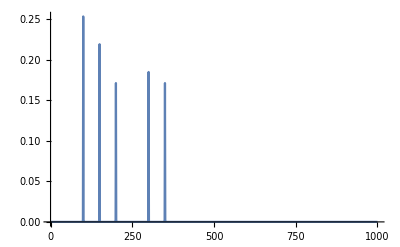

```mathematica
Rcvec=PoreDistribution[Nincl,diameter,distribData];
```

```mathematica
volfrac=0.6;
inctot=Nincl;
Ainc=Total[N[Pi*(Rcvec*Rcvec)]];
AT=Ainc /volfrac;
L=Sqrt[AT];
Print["Lato RVE:", L *1000," pixel"]
Counts[Rcvec*2]
Length[Rcvec]
Print[Rcvec];
```

Lato RVE:3441.86 pixel

<|0.6→6,0.4→9,0.3→8,0.7→9,0.2→8|>

40

{0.3,0.2,0.15,0.35,0.1,0.15,0.1,0.35,0.1,0.2,0.15,0.3,0.2,0.35,0.3,0.35,0.1,0.15,0.15,0.2,0.35,0.3,0.15,0.3,0.2,0.15,0.35,0.2,0.1,0.2,0.2,0.1,0.35,0.2,0.1,0.1,0.3,0.15,0.35,0.35}

```mathematica
Clear[center]
Clear[radi]
center=Import["centers.mat"];
center=Flatten[center,1];
center⟦1⟧
radi=Import["radii.mat"];
radi=Flatten[radi];
radi⟦1⟧
Length[center]
Length[radi]
```

{3.32,3.3}

0.1

40

40

{{3.32,3.3},{1.56,1.55},{0.2,2.65},{0.87,2.69},{2.33,1.36},{0.92,0.19},{2.6,2.26},{0.77,1.88},{2.46,0.65},{2.9,0.9},{0.14,1.19},{2.45,3.27},{3.22,2.55},{0.38,0.99},{1.46,3.24},{1.66,2.38},{0.23,1.98},{0.77,0.94},{2.58,1.05},{1.07,3.2},{2.57,1.68},{2.45,0.24},{1.93,0.24},{2.5,2.63},{3.08,1.29},{1.31,2.71},{0.57,2.33},{2.13,2.26},{1.22,1.25},{1.98,1.65},{0.49,3.05},{3.08,2.03},{1.98,0.9},{0.45,0.44},{2.95,3.01},{3.03,0.39},{1.98,3.01},{0.52,1.5},{1.31,1.98},{1.31,0.55}}

{0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.2,0.2,0.2,0.2,0.2,0.2,0.3,0.3,0.3,0.3,0.3,0.3,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35}

(-3.32+x)^2+(-3.3+y)^2≥0.01&&(-1.56+x)^2+(-1.55+y)^2≥0.01&&(-1.56+x)^2+(-1.55+y)^2≥0.01&&(-0.2+x)^2+(-2.65+y)^2≥0.01&&(-3.32+x)^2+(-3.3+y)^2≥0.01&&(-1.56+x)^2+(-1.55+y)^2≥0.01&&(-0.2+x)^2+(-2.65+y)^2≥0.01&&(-3.32+x)^2+(-3.3+y)^2≥0.01&&(-1.56+x)^2+(-1.55+y)^2≥0.01&&(-0.2+x)^2+(-2.65+y)^2≥0.01&&(-0.87+x)^2+(-2.69+y)^2≥0.01&&(-2.33+x)^2+(-1.36+y)^2≥0.01&&(-0.92+x)^2+(-0.19+y)^2≥0.01&&(-2.6+x)^2+(-2.26+y)^2≥0.01&&(-0.77+x)^2+(-1.88+y)^2≥0.01&&(-2.46+x)^2+(-0.65+y)^2≥0.01&&(-2.9+x)^2+(-0.9+y)^2≥0.01&&(-0.14+x)^2+(-1.19+y)^2≥0.01&&(-2.45+x)^2+(-3.27+y)^2≥0.0225&&(-3.22+x)^2+(-2.55+y)^2≥0.0225&&(-0.38+x)^2+(-0.99+y)^2≥0.0225&&(-1.46+x)^2+(-3.24+y)^2≥0.0225&&(-1.66+x)^2+(-2.38+y)^2≥0.0225&&(-0.23+x)^2+(-1.98+y)^2≥0.0225&&(-0.77+x)^2+(-0.94+y)^2≥0.0225&&(-2.58+x)^2+(-1.05+y)^2≥0.04&&(-1.07+x)^2+(-3.2+y)^2≥0.04&&(-2.57+x)^2+(-1.68+y)^2≥0.04&&(-2.45+x)^2+(-0.24+y)^2≥0.04&&(-1.93+x)^2+(-0.24+y)^2≥0.04&&(-2.5+x)^2+(-2.63+y)^2≥0.04&&(-3.08+x)^2+(-1.29+y)^2≥0.09&&(-1.31+x)^2+(-2.71+y)^2≥0.09&&(-0.57+x)^2+(-2.33+y)^2≥0.09&&(-2.13+x)^2+(-2.26+y)^2≥0.09&&(-1.22+x)^2+(-1.25+y)^2≥0.09&&(-1.98+x)^2+(-1.65+y)^2≥0.09&&(-0.49+x)^2+(-3.05+y)^2≥0.1225&&(-3.08+x)^2+(-2.03+y)^2≥0.1225&&(-1.98+x)^2+(-0.9+y)^2≥0.1225&&(-0.45+x)^2+(-0.44+y)^2≥0.1225&&(-2.95+x)^2+(-3.01+y)^2≥0.1225&&(-3.03+x)^2+(-0.39+y)^2≥0.1225&&(-1.98+x)^2+(-3.01+y)^2≥0.1225&&(-0.52+x)^2+(-1.5+y)^2≥0.1225&&(-1.31+x)^2+(-1.98+y)^2≥0.1225&&(-1.31+x)^2+(-0.55+y)^2≥0.1225

-Graphics-

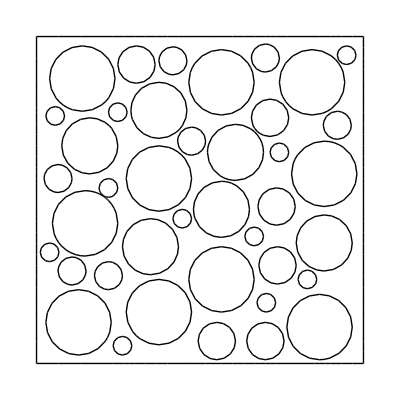

```mathematica
Clear[center]
Clear[radi]
L=3.5;
Lx = L; 
Ly = L; 
(*
center=Import["centers.mat"];
center=Flatten[center,1];*)
center=Import["centers.mat"];
center=Flatten[center,1]

radi=Import["radii.mat"];
radi=Flatten[radi]
(*
Ωext=Rectangle[{0,0},{Lx,Ly}];
    Ω=Ωext;
*)


mark=Length[radi];
(*
Do[
  Ω=RegionDifference[  Ω,Disk[center⟦i⟧, {radi⟦i⟧,radi⟦i⟧}]];
,{i,1,mark}];
*)
(*condition=(x-center⟦1,1⟧)^2+(y-center⟦1,2⟧)^2>=radi⟦1⟧^2&&(x-center⟦2,1⟧)^2+(y-center⟦2,2⟧)^2>=radi⟦2⟧^2*)


Do[
 condition=And[condition,(x-center⟦i,1⟧)^2+(y-center⟦i,2⟧)^2>=radi⟦i⟧^2];
,{i,1,mark}];
condition

 Ω=ImplicitRegion[condition,{{x,0,L},{y,0,L}}];
(*RegionPlot[Ω]*)
marker={{{Lx/100,Ly/100},1}};

Do[
marker=Join[marker,{{center⟦i⟧,2}}]
,{i,1,mark}];
(*
RegionPlot[Ω]
*)
(*
RegionBounds[Ω]
*)
mesh=ToElementMesh[Ω,{ {0,L},{0,L}},"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1];

(*
mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1,"MaxCellMeasure"->meshing,"MaxBoundaryCellMeasure"->meshingbound];*)
(*
im=-Graphics-;

dim=ImageDimensions[im]
Lx = dim⟦1⟧ 
Ly =dim⟦2⟧
mesha=ImageMesh[im]
mesh=ToElementMesh[mesha,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1];
*)
(*RegionPlot[Ω]*)
(*mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1,"MaxCellMeasure"->meshing,"MaxBoundaryCellMeasure"->meshingbound];*)
(*mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1];*)
(*
mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1,"MaxCellMeasure"->meshing,"MaxBoundaryCellMeasure"->meshingbound];
(*mesh=ToElementMesh[Ωext,"MeshOrder"->1,"RegionMarker"->{{{Lx/100,Ly/100},1}},"MeshElementType"->TriangleElement,"MaxCellMeasure"->0.01];
*)
mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1];*)
%["Wireframe"["MeshElement"->"BoundaryElements"]]
(*%["Wireframe"]*)
```

```mathematica
VoigtReussTest[verbOutput_,ℚ_,materialProp_,volfrac_]:=(
Emat1=materialProp⟦1,1⟧;
νmat1=materialProp⟦1,2⟧;
Emat2=materialProp⟦2,1⟧;
νmat2=materialProp⟦2,1⟧;
𝕊calc[mater_]:=(
𝕊materiale=DiagonalMatrix[{1/mater⟦1⟧,1/mater⟦1⟧,1/mater⟦1⟧,2(1+mater⟦2⟧)/mater⟦1⟧,2(1+mater⟦2⟧)/mater⟦1⟧,2(1+mater⟦2⟧)/mater⟦1⟧}];
𝕊materiale⟦1,2⟧=-(mater⟦2⟧/mater⟦1⟧);𝕊materiale⟦1,3⟧=-(mater⟦2⟧/mater⟦1⟧);
𝕊materiale⟦2,1⟧=-(mater⟦2⟧/mater⟦1⟧);𝕊materiale⟦2,3⟧=-(mater⟦2⟧/mater⟦1⟧);
𝕊materiale⟦3,1⟧=-(mater⟦2⟧/mater⟦1⟧);𝕊materiale⟦3,2⟧=-(mater⟦2⟧/mater⟦1⟧);
Return[𝕊materiale];
);
𝕊rid[𝕊𝕊_]:=(
Sridotta=DiagonalMatrix[{0,0,0}];
Do[
Sridotta⟦i,j⟧=𝕊𝕊⟦i,j⟧,{i,1,2},{j,1,2}];
Sridotta⟦3,3⟧=𝕊𝕊⟦6,6⟧;
Return[Sridotta];
);
fracweigth[M1_,M2_,frac_]:=(
M=M1*(1-frac)+M2*frac;
Return[M]
);

𝕊materiale1=𝕊calc[{Emat1,νmat1}];
ℂmateriale1=Inverse[𝕊materiale1];
𝕊materiale2=𝕊calc[{Emat2,νmat2}];
ℂmateriale2=Inverse[𝕊materiale2];
𝕊mat1=𝕊rid[𝕊materiale1];
𝕊mat2=𝕊rid[𝕊materiale2];
ℂmat1=𝕊rid[ℂmateriale1];
ℂmat2=𝕊rid[ℂmateriale2];
ℂvoigt=fracweigth[ℂmateriale1,ℂmateriale2,volfrac];
𝕊reuss=fracweigth[𝕊materiale1,𝕊materiale2,volfrac];

ℂreuss=Inverse[𝕊reuss];
ℂvoigt=𝕊rid[ℂvoigt];
ℂreuss=𝕊rid[ℂreuss];

;
CLiminf=ℚ-ℂreuss;
CLimsup=ℂvoigt - ℚ;
check1=PositiveDefiniteMatrixQ[CLiminf];
check2=PositiveDefiniteMatrixQ[CLimsup];
If[And[check1,check2],StylePrint["Reuss and Voigt lim is verified",FontColor->Green],StylePrint["Lim not verified",FontColor->Red]];
If[Not[check1],Print["Reuss failed"]];
If[Not[check2],Print["Voigt failed"]];

If[verbOutput, 
Print["𝕔mat1: ",N[MatrixForm[ℂmat1]],"  ","𝕤mat1: ",N[MatrixForm[𝕊mat1]]];
Print["𝕔mat2: ",N[MatrixForm[ℂmat2]],"  ","𝕤mat2 : ",N[MatrixForm[𝕊mat2]]];
Print[Subscript["𝕔","Voigt"],": ",MatrixForm[ℂvoigt]];
Print[Subscript["𝕔","Reuss"],": ",MatrixForm[ℂreuss]];
];
StylePrint["",FontColor->Black];
);

Checkconvergence[meshprop_,meshingbound_,verboseOutput_,DebugVal_,iteration_]:=(
testBC={{1,0,0},{0,0,1},{0,0.5,0}}; (*non sono le ϵ ma valori di comodo per i parametri a,b,c per le BC tipo essenziale*)
ℂcol={{0,0,0},{0,0,0},{0,0,0}};
materialprop={{5000,0.3},{0.15,0.1}}; (* E, ν material *)
(*
Emat1=5000;
νmat1=0.3;*)

(*
Emat2=0.15;
νmat2=0.1;
*)
Do[
ℂcol⟦i⟧=TEST[testBC⟦i⟧,meshprop,meshingbound,materialprop];
,{i,1,3}]
ℂcol;
ℚ=Transpose[ℂcol];
Print[Subscript["ℂ",StringJoin["om",ToString[iteration]]],": ",MatrixForm[ℚ]];
Export[StringJoin[NotebookDirectory[],"C_om_",ToString[iteration],".tex"],MatrixForm[ℚ]];

If[DebugVal,(* set it to true only IF TESTING ISOTROPIC MATERIAL !!!!*)
solved1=SolveValues[E1*(1-ν12)/((1 -2*ν12)(1+ν12))==ℚ⟦1,1⟧&&E1*ν12/((1 -2*ν12)(1+ν12))==ℚ⟦1,2⟧,{E1,ν12}];
solved2=SolveValues[E2*(1-ν21)/((1 -2*ν21)(1+ν21))==ℚ⟦2,2⟧&&E2*ν21/((1 -2*ν21)(1+ν21))==ℚ⟦2,1⟧,{E2,ν21}];
EE1=solved1⟦1,1⟧;
νν12=solved1⟦1,2⟧;
νν21=solved2⟦1,2⟧;
EE2=solved2⟦1,1⟧;
Print[Subscript["E","1"],"=",EE1] ;
Print[Subscript["E","2"],"=",EE2] ;
Print[Subscript["ν","12"],"=",νν12]; 
Print[Subscript["ν","21"],"=",νν21] ;
Print[Subscript["G","12"],"=",ℚ⟦3,3⟧];     (*VERIFICA COSA SUCCEDE PER L'ANISOTROPIA*)
Print["Verifica per l'isotropia ",Subscript["G","12"],":",EE1/(2*(1+νν12))];
];

(* set VerboseOutpu-> True to obtain material properties*)
VoigtReussTest[verboseOutput,ℚ,materialprop,volfrac];
normℚ=Tr[Transpose[ℚ].ℚ];
Return[{ℂcol⟦1,1⟧,normℚ}];
)

TEST[test_,meshprop_,meshingbound_,materialProp_]:=(
<<AceFEM`;
SMTInputData[];
(* define geometry properties from previous section*)
(*mesh=GeometrySet[meshprop,meshingbound];*)
(* define material properties*)

(*domain={{"T1 matrix",5000,0.3},{"T1 inc 1",0.15,0.1}}; (*taken from lit (3800+6600/)2*)*)

Emat1=materialProp⟦1,1⟧;
νmat1=materialProp⟦1,2⟧;
Emat2=materialProp⟦2,1⟧;
νmat2=materialProp⟦2,1⟧;


domain={{"T1 matrix",Emat1,νmat1},{"T1 inc 1",Emat2,νmat2}}; 
DomainProp[domain];
SMTAddMesh[mesh,{{"T1",1}->"T1 matrix",
{"T1",2}->"T1 inc 1"
}];
a=test⟦1⟧;
b=test⟦2⟧;
c=test⟦3⟧;
SMTAddEssentialBoundary[Line[{{0,0},{0,Ly}}], 1->Function[{n, X, Y},b Y], 2 ->Function[{n, X, Y},c Y],"Set"->True];
SMTAddEssentialBoundary[Line[{{0,Ly},{Lx,Ly}}], 1 -> Function[{n, X, Y}, b*Ly+a*X], 2->Function[{n, X, Y}, c*Ly+b*X],"Set"->True];
SMTAddEssentialBoundary[Line[{{Lx,Ly},{Lx,0}}], 1 ->Function[{n, X, Y}, a*Lx+b*Y], 2->Function[{n, X, Y}, b*Lx+c*Y], "Set"->True];
SMTAddEssentialBoundary[Line[{{0,0},{Lx,0}}], 1 ->Function[{n, X, Y},a*X], 2-> Function[{n, X, Y}, b*X], "Set"->True];
SMTAnalysis[];

SMTNextStep["λ"->1];
SMTNewtonIteration[];
(*Check convergence*)
SMTNewtonIteration[];
tolNR=10^-8; maxNR = 15;
SMTConvergence[tolNR,maxNR,"Analyze"];
SMTShowMesh["Mesh"->RGBColor[0,0,0],"FillElements"->{RGBColor[0.650,0.486,0.321],RGBColor[0.756,0.152,0.176]}];
Show[
SMTShowMesh["Field"->"σyy","DeformedMesh"->True,"Mesh"->GrayLevel[0.9]],
SMTShowMesh["FillElements"->False,"BoundaryConditions"->True,"Mesh"->GrayLevel[0]]];
area=Lx*Ly;
nel = SMTNoElements;
column=Total[Table[SMTElementData[i, "Data"], {i, nel}]]/area;
Return[column];
)

DomainProp[domainparam_]:=(
parameter={ToString[domainparam⟦1,1⟧],"T1LE",{"E *"->domainparam⟦1,2⟧,"ν *"->domainparam⟦1,3⟧}};
Do[
parameter=Join[{parameter},{{ToString[domainparam⟦i,1⟧],"T1LE",{"E *"->domainparam⟦i,2⟧,"ν *"->domainparam⟦i,3⟧}}}]
,{i,2,Length[domainparam]}];
SMTAddDomain[
parameter
];
)
```

### Automatic solution

```mathematica
C11=Table[0*i,{i,1,Length[meshing]}];
CC=Table[0*i,{i,1,Length[meshing]}];
timecalc=Table[0*i,{i,1,Length[meshing]}];
vec=Table[{0*i,0,j},{i,1,Length[meshing]},{j,1,2}];
vecandNorm=Table[{0*i,0,j},{i,1,Length[meshing]},{j,1,2}];
Do[
timecalc⟦i⟧=Timing[
{C11⟦i⟧,CC⟦i⟧}=Checkconvergence[meshing⟦i⟧,meshingbound⟦i⟧,False,False,i];
Export[StringJoin[NotebookDirectory[],"test","_mesh_",ToString[i],".png"],SMTShowMesh["Mesh"->RGBColor[0,0,0],"FillElements"->{RGBColor[0.650,0.486,0.321],RGBColor[0.756,0.152,0.176]}],ImageResolution->300];
];
vec⟦i,1⟧=2*Length[SMTPostData["u"]];
vec⟦i,2⟧=C11⟦i⟧;
vecandNorm⟦i,1⟧=2*Length[SMTPostData["u"]];
vecandNorm⟦i,2⟧=CC⟦i⟧;
,{i,1,Length[meshing]}]
Print[Subscript["C","11"],": ",Transpose[vec]⟦2⟧];
Export[StringJoin[NotebookDirectory[],"C11.tex"],Transpose[vec]⟦2⟧];
Print["norm C: ",Transpose[vecandNorm]⟦2⟧];
Export[StringJoin[NotebookDirectory[],"normC.tex"],Transpose[vecandNorm]⟦2⟧];
Print["Gradi di libertà: ",Transpose[vec]⟦1⟧];
Export[StringJoin[NotebookDirectory[],"gradi_liberta.tex"],Transpose[vec]⟦1⟧];
Print["Tempi di calcolo: ",Transpose[timecalc]⟦1⟧," in sec"];
Export[StringJoin[NotebookDirectory[],"tempi_calcolo_s.tex"],Transpose[timecalc]⟦1⟧];
Print["Tempi di calcolo: ",Transpose[timecalc]⟦1⟧/60," in min"];
(*Checkconvergence[meshdimension,verboseOutput,DebugVal,iteration];*)
```

Reuss and Voigt lim is verified

Tempi di calcolo: {0.0479167} in min

Tempi di calcolo: {2.875} in sec

Gradi di libertà: {3048}

norm C: {3.52573×10^6}

C_11: {1213.18}

ℂ_om1: (1213.18 | 403.493 | 43.404
403.493 | 1281.54 | 20.7354
43.404 | 20.7354 | 285.233)

vec